# FIG. 1: One-dimensional potential energy barrier of height "V_0" and width "a"

```mathematica
V[x_]=Piecewise[{{Subscript[V, 0], 0≤x≤a}, {0, True}}]/.Subscript[V, 0]->7;
```

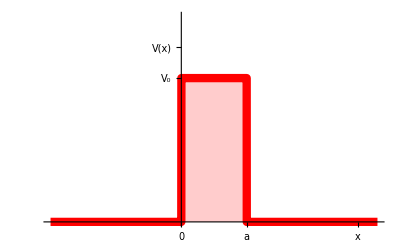

```mathematica
Plot[{V[x]/.{a->3}},{x,-6,9},
PlotRange->{{-6,9},{0.0,10}},
BaseStyle->{FontFamily->"Helvetica",FontSize->17},
PlotStyle->{Red,Thickness@0.015},
AxesStyle->Arrowheads[{0.0,0.04}],
Filling->Axis,
Ticks->{{{0.0,"0"},{3,"a"},{8.1,"x"}},{{7,"V_0"},{8.5,"V(x)"}}}]
```

Using drawing tools to define the regions, the following plot was obtained .